## Polygonalize-Example.nb

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Tue 13 Jun 2017 11:33:08
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
T=CSVToTissue["meristem.csv"];
```

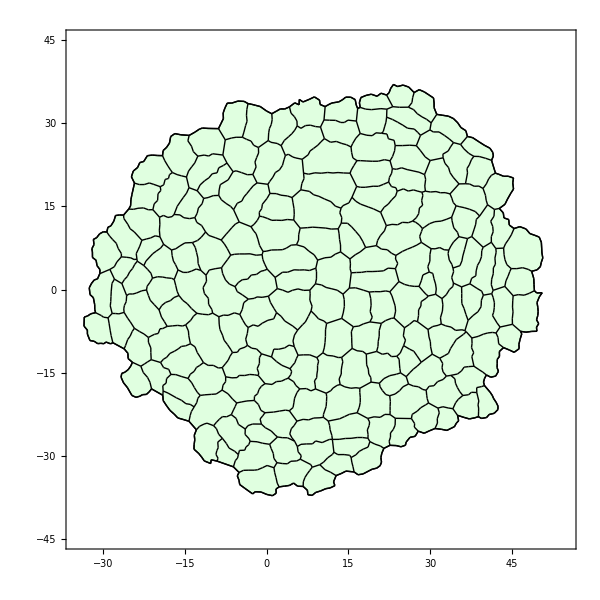

```mathematica
ShowTissue[T, Frame-> True, PlotRange-> {{-35,55},{-45,45}}, ImageSize-> 600]
```

```mathematica
Q=Polygonalize[T];
```

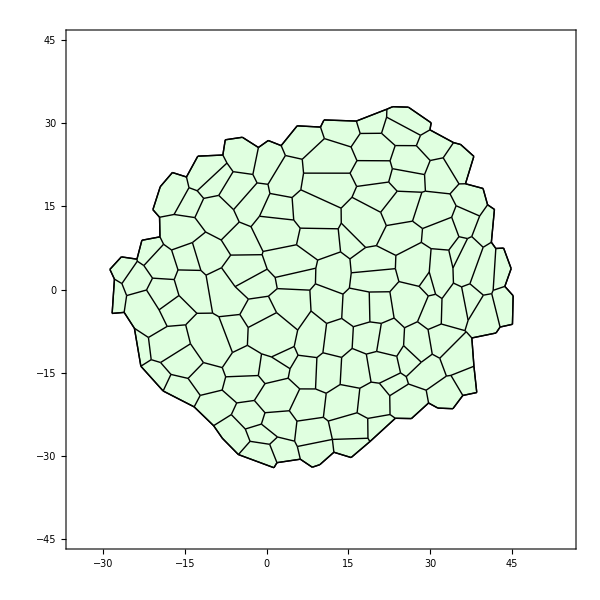

```mathematica
ShowTissue[Q, Frame-> True, PlotRange-> {{-35,55},{-45,45}}, ImageSize-> 600]
```